```mathematica
ClearAll["Global`*"]
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_]:=Sin[2 π x^2/L^2]
Lu[x_]:=(4 π (L^2 Cos[(2 π x^2)/L^2]-4 π x^2 Sin[(2 π x^2)/L^2]))/L^4
gradu[x_]:=(4 π x Cos[(2 π x^2)/L^2])/L^2
```

```mathematica
L=1;
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/periodic/solution/nodal_values/u.csv"][[2;;]];
(*the solution obtained from finite elements is not unique -> it is determined up to a constant-> substract it off so you can compare with the exact one*)
t0=t[[1,1]];
t=Table[{t[[i,2]],t[[i,1]]-0 t0},{i,2,Length[t]}]
```

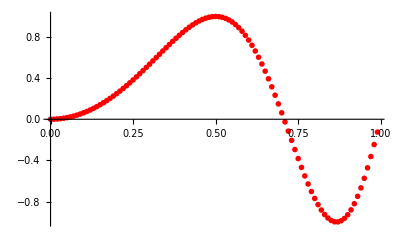

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

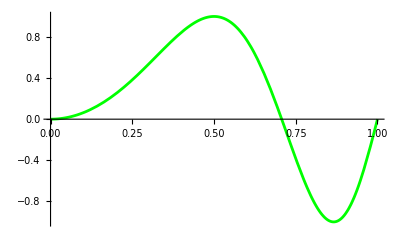

```mathematica
plotexact=Plot[u[x],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

0.000928795

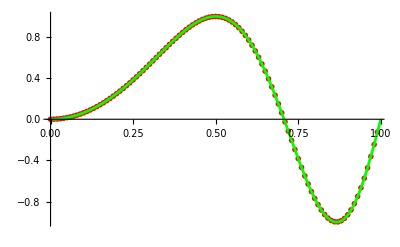

```mathematica
Show[plotnum,plotexact]
```